```mathematica
(*Capacitante function parameters*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
threshold=0;maxtime=1000;plottime=300;
case=3;point=3;
Switch[case,
1,C0=1;T=50;τ2=0.5;τ4=1;prefix="Fig8a_";
pointList={{{0.05,0.6}},{{0.25,0.5}},{{0.25,0.7}}};,
2,C0=1;T=20;τ2=0.5;τ4=1;prefix="Fig8b_";
pointList={{{0.05,0.85}},{{0.25,0.5}},{{0.25,0.9}}};,
3,C0=1;T=0.5;τ2=0.5;τ4=1;prefix="Fig8c_";
pointList={{{0.05,0.7}},{{0.25,0.5}},{{0.25,0.9}}};
]
Switch[point,
1,δ=pointList[[1]][[1]][[1]];C1=pointList[[1]][[1]][[2]];filename=prefix<>"example1.png";,
2,δ=pointList[[2]][[1]][[1]];C1=pointList[[2]][[1]][[2]];filename=prefix<>"example2.png";,
3,δ=pointList[[3]][[1]][[1]];C1=pointList[[3]][[1]][[2]];filename=prefix<>"example3.png";
];
{τ1,τ3}={0.1+δ,0.6+δ};
(*HH Parameters from Weinberg*)
αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Vrest=-65; (*Weinberg uses -80, but it seems to be *)
mrest=0.05;
hrest=0.596;
nrest=0.315;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;
(*Ionic Chanels*)
Am[V_]=αm (V-Vαm)/(1-Exp[-(V-Vαm)/Kαm]);
Bm[V_]=βm Exp[-(V-Vβm)/Kβm];
Ah[V_]=αh Exp[-(V-Vαh)/Kαh];
Bh[V_]=βh/(1+Exp[-(V-Vβh)/Kβh]);
An[V_]=αn (V-Vαn)/(1-Exp[-(V-Vαn)/Kαn]);
Bn[V_]=βn Exp[-(V-Vβn)/Kβn];
```

```mathematica
(*Solving HH*)

Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(C1-C0)(Mod[t,T]-τ1 T)/((τ2-τ1)T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T] - τ3 T)(C0-C1)/((τ4-τ3)T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/((τ2-τ1)T),Mod[t,T]< τ3 T,0, True,(C0-C1)/((τ4-τ3)T)];
(*Solving HH*)
{U,M,H,NN}=NDSolveValue[{u'[t]==-gNa m[t]^3 h[t](u[t]/Ct[t]-Vrest-ENa)-gK n[t]^4(u[t]/Ct[t]-Vrest-EK) -gL(u[t]/Ct[t]-Vrest-EL),
m'[t]==Am[u[t]/Ct[t]-Vrest](1-m[t])-Bm[u[t]/Ct[t]-Vrest]m[t],
h'[t]==Ah[u[t]/Ct[t]-Vrest](1-h[t])-Bh[u[t]/Ct[t]-Vrest] h[t],
n'[t]==An[u[t]/Ct[t]-Vrest](1-n[t])-Bn[u[t]/Ct[t]-Vrest]n[t],
u[0]==Ct[0]*Vrest,m[0]==mrest,h[0]==hrest,n[0]==nrest},
{u,m,h,n},{t,0,maxtime}];
```

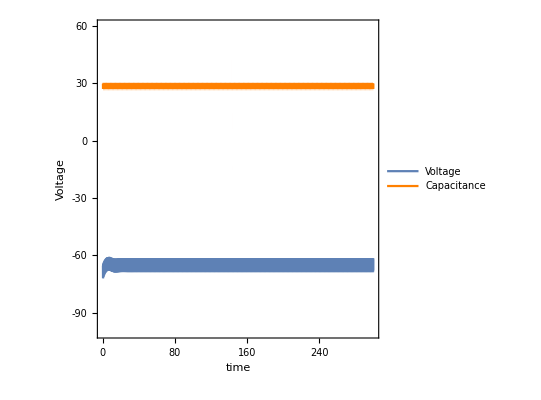

Fig8c_example3.png

```mathematica
(*Visualization*)
frange={-100,60};
grange={-100/30,60/30};
voltage=Plot[U[t]/Ct[t],{t,0,plottime},
PlotRange->frange,
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16],
MaxRecursion->3,
PlotPoints->10000
];
capacitance=Plot[{Ct[t]},{t,0,plottime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];

fticks=FindDivisions[Append[frange,30],10];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
(*gticks=FindDivisions[Append[grange,0.5],10];*)
g1=Legended[
Show[voltage, capacitance/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],
AspectRatio->1,
FrameTicks->{{fticks,gticks},{Automatic,Automatic}}],
Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},
{Style["Voltage",FontSize->18],
Style["Capacitance",FontSize->18]}
,LegendLayout->"Row"],
{{0.5,0.95}}]
]

Export[filename,g1]
```